Autor: Radosław Terelak

# Metody numeryczne

## (kierunek Informatyka)

## Projekt 6

Aproksymacja średniokwadratowa dyskretna

Napisać procedurę realizującą algorytm aproksymacji średniokwadratowej dyskretnej. 
Działanie procedury przetestować na przykładzie z wykładu.

a) Aproksymować punkty (x_i, sin x_i) dla x_i=0,1,...,11,12, wielomianem stopnia trzeciego. Jako funkcję wagową raz przyjąć funkcję w(x)=1, natomiast drugi raz funkcję w(x)={10 | dla x∈[3,7],
10^-10 | dla x∈[0,3)∪(7,12].
Wykreślić na wspólnym rysunku otrzymane wielomiany oraz punkty aproksymacji.

b) Zmianę  temperatury płynu w zbiorniku ilustruje następująca tabela:

t[s] | 0 | 25 | 50 | 75 | 100 | 125 | 150
T[°C] | 90 | 80 | 71 | 63 | 57 | 51 | 46

Aproksymować temperaturę funkcją postaci T(t)=a exp(b  t). Jako funkcję wagową przyjąć w(t)=1.
Wyznaczyć czas w którym temperatura płynu będzie równa 20°C.

## Rozwiązanie

### Program

```mathematica
Clear["Global`*"];
φ[0][x_]:=1;
φ[i_][x_]:=x^i;
```

```mathematica
aproksymacja [φ_,xa_,ya_,st_,w_]:=Module [{n,l,f,d,i,j,k,a,F},
n=st+1;
l=Length[xa];
f=Table[0,{n}];
For[k=1,k≤n,k++,
f⟦k⟧=∑_(j=1)^l (w[xa⟦j⟧]*ya⟦j⟧*φ[(k-1)][xa⟦j⟧]);
];

d=Table[0,{n},{n}];
For[i=1,i≤n,i++,
For[k=1,k≤n,k++,
d⟦i,k⟧=∑_(j=1)^l (w[xa⟦j⟧]*φ[i-1][xa⟦j⟧]*φ[k-1][xa⟦j⟧]);
];
];
a=LinearSolve[d,f];
F=0;
For[i=1,i≤Length[a],i++,
F=F+a⟦i⟧*φ[i-1][x];
];
Simplify[F];
(* Print["F(x) = ",F]; *)
Return[F];
]
```

### Przykład testowy

```mathematica
x1={0,1,2,3};
y1={1,-1,2,4};
w[x_]:=1;
aproksymacja[φ,x1,y1,2,w]
```

7/10-(9 x)/5+x^2

### Zadanie a)

```mathematica
Clear[w1, xa, ya, Zad1a, rys1];
w1[x_]:=1;
xa=Table[i,{i,0,12,1}];
ya=Table[Sin[xa[[i]]],{i,1,13,1}];
Zad1a=aproksymacja[φ,xa,ya,3,w1] //N
rys1 = Plot[Zad1a,{x,xa⟦1⟧,xa⟦Length[xa]⟧},PlotStyle->Red];
```

0.632651-0.443524 x+0.0895692 x^2-0.00525558 x^3

10.4317-5.7181 x+0.873654 x^2-0.0365756 x^3

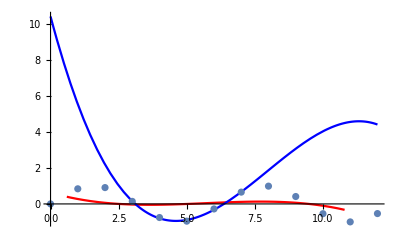

```mathematica
Clear[w2, Zad1b, rys2];
w2[x_]:=10/;3≤x≤7
w2[x_]:=10^-10
Zad1b=aproksymacja[φ,xa,ya,3,w2] //N
rys2 = Plot[Zad1b,{x,xa⟦1⟧,xa⟦Length[xa]⟧},PlotStyle->Blue];
Show[rys1,rys2,ListPlot[Thread[{xa,ya}]],PlotRange->All]
```

### Zadanie b)

4.49162-0.00447648 x

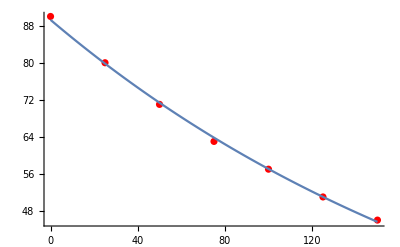

{{x→334.166}}

```mathematica
Clear[t,T,w1,dane,rys1,logT,ZadB,a,b,c,fN,rys2];
t={0,25,50,75,100,125,150};
T={90,80,71,63,57,51,46};
w1[x_]:=1;
dane=Transpose[{t,T}];
rys1=ListPlot[{dane},PlotStyle->{Red}];
logT=Log[T];
ZadB=aproksymacja[φ,t,logT,1,w1] //N
c=ZadB⟦1⟧;
b=ZadB⟦2,1⟧;
a=Exp[c];
fN[xn_]:=a Exp[b*xn]
rys2=Plot[fN[x],{x,t⟦1⟧,t⟦Length[t]⟧}];
Show[rys1,rys2, PlotRange->All]
NSolve[fN[x]==20,x,Reals]
```